# MODELACIÓN DE UNA SITUACIÓN REAL

```mathematica
ClearAll["Global'*"]
```

```mathematica
datos={{0,90},{2,78},{4,79},{6,62},{8,56},{10,52}}
```

{{0,90},{2,78},{4,79},{6,62},{8,56},{10,52}}

```mathematica
aj=NonlinearModelFit[datos,25+dT Exp[-k t],{{dT,60},{k,0.1}},t]
```

FittedModel[25+65.9023 ⅇ^(-0.087093 t)]

```mathematica
?NonlinearModelFit
```

va con [datos, funcion, {{variable fija 1 ,empieza con este numero},{varuable fija 2,empieza con este numero}, variable]

```mathematica
aj["BestFitParameters"]
aj[15]
```

{dT→65.9023,k→0.087093}

42.846

FittedModel[25+65.9023 ⅇ^(-0.087093 t)]

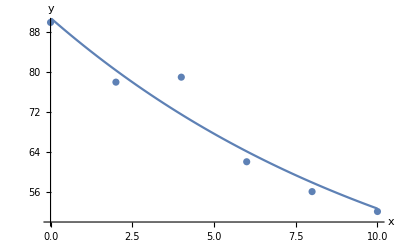

```mathematica
Show[ListPlot[datos],Plot[aj[t],{t,0,10}],AxesLabel->{"x","y"}]
```

```mathematica
FindRoot[aj[t]==35,{t,15}]
```

{t→21.6503}

# series

LA FUNCION NORMAL NORMALIZA A FUNCION LA SERIES

```mathematica
Series[Sin[x],{x,0,50}];
```

```mathematica
n=Normal[Series[Sin[x],{x,0,50}]];
```

General::munfl: (3.49359×10^-236 (-1))/138683118545689835737939019720389406345902876772687432540821294940160000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.64492×10^-244)/507580213877224798800856812176625227226004528988036003099405939480985600000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.80281×10^-252 (-1))/1982608315404440064116146708361898137544773690227268628106279599612729753600000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

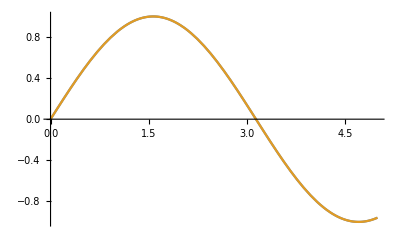

```mathematica
Plot[{Sin[x],n},{x,0,5}]
```

# algebra lineal

```mathematica
ClearAll["Global'*"]
```

```mathematica
Eigensystem[{{1,2},{4,1}}]
```

{{1+2 √2,1-2 √2},{{1/(√2),1},{-1/(√2),1}}}

# Ecuaciones Diferenciales

```mathematica
j=DSolve[ {y''[t]+2*y'[t]+5*y[t]==0,y[0]==1,y'[0]==0},y[t],t
]
```

{{y[t]→1/2 ⅇ^-t (2 Cos[2 t]+Sin[2 t])}}

```mathematica
DSolveValue[{y''[t]+2*y'[t]+5*y[t]==0,y[0]==1,y'[0]==0},y[t],t]
```

1/2 ⅇ^-t (2 Cos[2 t]+Sin[2 t])

```mathematica
f=D[j,t]
```

{{y'[t]→1/2 ⅇ^-t (2 Cos[2 t]-4 Sin[2 t])-1/2 ⅇ^-t (2 Cos[2 t]+Sin[2 t])}}

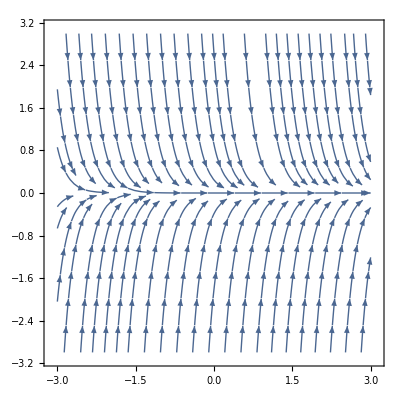

```mathematica
StreamPlot[{1, 2*y'[t] - 5y}, {t, -3, 3}, {y, -3, 3}]
```

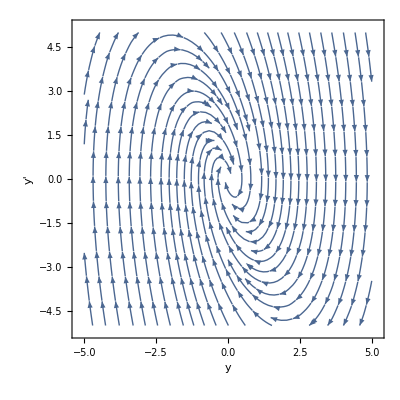

```mathematica
StreamPlot[{v,-2*v-5*y},{y,-5,5},{v,-5,5},AxesLabel->{"y","y'"}]
```

```mathematica
f=D[j,t]
j=DSolve[ {y''[t]+2*y'[t]+5*y[t]==0,y[0]==1,y'[0]==0},y[t],t
]
```

{{y'[t]→1/2 ⅇ^-t (2 Cos[2 t]-4 Sin[2 t])-1/2 ⅇ^-t (2 Cos[2 t]+Sin[2 t])}}

{{y[t]→1/2 ⅇ^-t (2 Cos[2 t]+Sin[2 t])}}

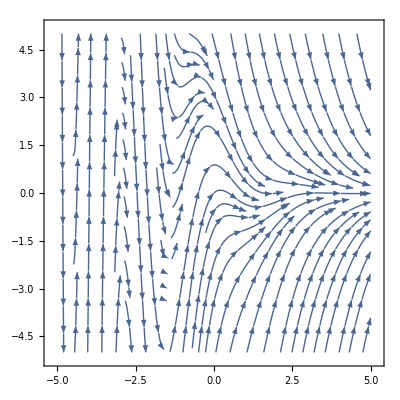

```mathematica
StreamPlot[{1,1/2*Exp[-t]*(2 Cos[2 t]-4 Sin[2 t])-y},{t,-5,5},{y,-5,5}]
```

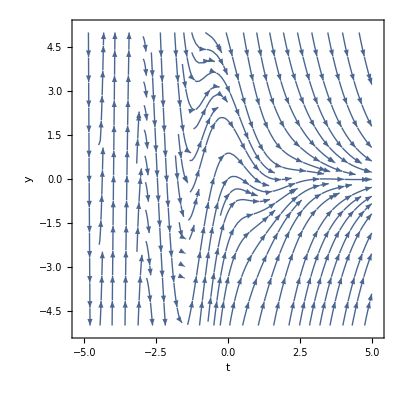

```mathematica
StreamPlot[{1, 1/2*Exp[-t]*(2*Cos[2*t] - 4*Sin[2*t]) - y}, {t, -5, 5}, {y, -5, 5}, AxesLabel -> {"t", "y"}]
```

```mathematica
ClearAll["Global'o"]
DSolve[y'[x] + 2*y[x] == 5*x, y'[x], x]
```

DSolve[2 y[x]+y'[x]==5 x,y'[x],x]